# Analyzing spectrum for Gaussian Ensembles

The idea of this  notebook is to analyze the properties of random matrices from the Gaussian ensembles: Gaussian Orthogonal Ensemble (GOE), Gaussian Symplectic Ensemble (GSE) and Gaussian Unitary Ensemble.

We will create functions that will generate random matrices from these ensembles. We will focus on computing and analyzing their eigenvalues. We know that for large enough matrices, the distribution of these eigenvalues should follow  Wigner’s Semicircle Law. Our first task will be to plot the empirical distribution of these eigenvalues and compare it with the Semicircle Law. We will also compare their empirical Cumulative Distribution Function (CDF) with the one expected from the Semicircle Law.

Finally, and more importantly, we will analyze the spacings (differences) between consecutive eigenvalues. In order to correctly analyze the spectrum of these matrices, we will first unfold it, taking as our fitting function Wigner’s Semicircle. We will then compute the (normalized) spacings between consecutive eigenvalues and plot their distribution. Since these matrix ensembles represent chaotic systems, the probability density function of the normalized spacings should follow Wigner’s surmise: p(s)=Piecewise[{{π/2 s e^(-(π s^2)/4), (GOE),}, {32/π^2 s^2 e^(-(4 s^2)/π), (GUE),}, {2^18/(3^6 π^3)s^4 e^((-64 s^2)/(9π)), (GSE).}}]

## Set Up Gaussian Orthogonal Ensemble

#### Generate a GOE matrix:

```mathematica
GOEMatrix[n_]:=Module[{X},X=RandomVariate[NormalDistribution[0,1],{n,n}];
(X+Transpose[X])/2];
```

#### Extract and sort the eigenvalues from GOE:

```mathematica
EigenvaluesGOE[matrixSize_]:=Module[{eigenvalues,matrix},
matrix=GOEMatrix[matrixSize];
eigenvalues=Sort[Eigenvalues[matrix]]]
```

#### Compute (empirical) CDF of the eigenvalues:

```mathematica
CDensityGOE[matrixSize_]:=Module[{cumulativeDensity,eigenvalues,i,x},eigenvalues=EigenvaluesGOE[matrixSize];x=Range[-RadiusGOE[matrixSize],RadiusGOE[matrixSize],RadiusGOE[matrixSize]/1000];cumulativeDensity={};i=1;
Do[cumulativeDensity=Join[cumulativeDensity,{Count[eigenvalues,_?(#<x[[i]]&)]/Length[eigenvalues]}];i=i+1,Length[x]];
cumulativeDensity]
```

#### Wigner’s Semicircle Law for GOE:

```mathematica
RadiusGOE[matrixSize_]:=√(2*matrixSize); (*Radius of the semicircle for this ensemble*)
```

```mathematica
SemicircleGOE[x_,matrixSize_]:=Piecewise[{{(2/(π *RadiusGOE[matrixSize]^2)) Sqrt[RadiusGOE[matrixSize]^2-x^2],Abs[x]<=RadiusGOE[matrixSize]},{0,True}}]
```

```mathematica
CDFSemicircleGOE[x_,matrixSize_]:=Piecewise[{{0,x<=-RadiusGOE[matrixSize]},{1/2+(x Sqrt[RadiusGOE[matrixSize]^2-x^2])/(π RadiusGOE[matrixSize]^2)+ArcSin[x/RadiusGOE[matrixSize]]/π,-RadiusGOE[matrixSize]<x<RadiusGOE[matrixSize]},{1,x>=RadiusGOE[matrixSize]}}](*CDF associated to Semicirlce*)
```

#### Unfolding and spacing:

```mathematica
UnfoldingGOE[eigenvalues_,matrixSize_]:=Table[CDFSemicircleGOE[x,matrixSize] ,{x,eigenvalues}]; (*Unfolds eigenvalues using the CDF of the semicircle's law*)
```

```mathematica
SpacingGOE[matrixSize_]:=Module[{AllSpacings,eigenvalues,unfoldedEigenvalues,spacings},AllSpacings={};
eigenvalues=EigenvaluesGOE[matrixSize];(*Generate matrix, compute and sort the eigenvalues*)
unfoldedEigenvalues=UnfoldingGOE[eigenvalues,matrixSize];(*Unfold eigenvalues*)
spacings=(matrixSize-1)*Differences[unfoldedEigenvalues]/(unfoldedEigenvalues[[matrixSize]]-unfoldedEigenvalues[[1]])] (*Compute normalized spacings for unfolded eigenvalues*)
```

## Set Up Gaussian Symplectic Ensemble

#### Generate a GSE matrix:

```mathematica
GSEMatrix[n_]:=Module[{Id,e1,e2,e3,Diagonal,OffDiagonal,blockMatrix},
(*Quaternionic basis matrices*)
Id={{1,0},{0,1}};
e1={{I,0},{0,-I}};
e2={{0,1},{-1,0}};
e3={{0,I},{I,0}};
Diagonal=RandomVariate[NormalDistribution[0,1/2],n];(*Diagonal random variables*)
OffDiagonal=Table[Module[{random,element},
random=RandomVariate[NormalDistribution[0,1/(2 Sqrt[2])],4];
element=random[[1]]*Id+random[[2]]*e1+random[[3]]*e2+random[[4]]*e3;
element],{i,n},{j,i-1}];(*Off-diagonal random quaternionic blocks*)
(*Assemble block matrix with Hermitian structure*)
blockMatrix=Table[Which[
i==j,Diagonal[[i]]*Id,(*Diagonal elements*)
i<j,ConjugateTranspose[OffDiagonal[[j,i]]], (*Lower triangular*)
True,OffDiagonal[[i,j]]],{i,n},{j,n}]; (*Upper triangular*)
ArrayFlatten[blockMatrix]]
```

#### Extract and sort the eigenvalues from GSE:

```mathematica
EigenvaluesGSE[matrixSize_]:=Module[{eigenvalues,matrix},
matrix=GSEMatrix[matrixSize];
eigenvalues=Sort[Re[Eigenvalues[matrix]]]]
```

#### Compute (empirical) CDF of the eigenvalues:

```mathematica
CDensityGSE[matrixSize_]:=Module[{cumulativeDensity,eigenvalues,i,x},eigenvalues=EigenvaluesGSE[matrixSize];x=Range[-RadiusGSE[matrixSize],RadiusGSE[matrixSize],RadiusGSE[matrixSize]/1000];cumulativeDensity={};i=1;
Do[cumulativeDensity=Join[cumulativeDensity,{Count[eigenvalues,_?(#<x[[i]]&)]/Length[eigenvalues]}];i=i+1,Length[x]];
cumulativeDensity]
```

#### Wigner’s Semicircle Law for GSE:

```mathematica
RadiusGSE[matrixSize_]:=√(2*matrixSize);(*Radius of the semicircle for this ensemble*)
```

```mathematica
SemicircleGSE[x_,matrixSize_]:=Piecewise[{{(2/(π *RadiusGSE[matrixSize]^2)) Sqrt[RadiusGSE[matrixSize]^2-x^2],Abs[x]<=RadiusGSE[matrixSize]},{0,True}}]
```

```mathematica
CDFSemicircleGSE[x_,matrixSize_]:=Piecewise[{{0,x<=-RadiusGSE[matrixSize]},{1/2+(x Sqrt[RadiusGSE[matrixSize]^2-x^2])/(π RadiusGSE[matrixSize]^2)+ArcSin[x/RadiusGSE[matrixSize]]/π,-RadiusGSE[matrixSize]<x<RadiusGSE[matrixSize]},{1,x>=RadiusGSE[matrixSize]}}] (*CDF associated to Semicirlce*)
```

#### Unfolding and spacing:

```mathematica
UnfoldingGSE[eigenvalues_,matrixSize_]:=Table[CDFSemicircleGSE[x,matrixSize] ,{x,eigenvalues}]; (*Unfolds eigenvalues using the CDF of the semicircle's law*)
```

```mathematica
SpacingGSE[matrixSize_]:=Module[{AllSpacings,eigenvalues,unfoldedEigenvalues,spacings},AllSpacings={};
eigenvalues=EigenvaluesGSE[matrixSize]; (*Generate matrix, compute and sort the eigenvalues*)
unfoldedEigenvalues=First@Transpose@Tally@N@Round[UnfoldingGSE[eigenvalues,matrixSize],10^-8];(*Unfold eigenvalues taking into account their multiplicities*)
spacings=(matrixSize-1)*Differences[unfoldedEigenvalues]/(unfoldedEigenvalues[[matrixSize]]-unfoldedEigenvalues[[1]])](*Compute normalized spacings for unfolded eigenvalues*)
```

## Set Up Gaussian Unitary Ensemble

#### Generate a GUE matrix:

```mathematica
GUEMatrix[n_]:=Module[{X},X=RandomVariate[NormalDistribution[0,1/√2],{n,n}]+I*RandomVariate[NormalDistribution[0,1/√2],{n,n}];
(X+Conjugate[Transpose[X]])/2]
```

#### Extract and sort the eigenvalues from GUE:

```mathematica
EigenvaluesGUE[matrixSize_]:=Module[{eigenvalues,matrix},
matrix=GUEMatrix[matrixSize];
eigenvalues=Sort[Re[Eigenvalues[matrix]]]]
```

#### Compute (empirical) CDF of the eigenvalues:

```mathematica
CDensityGUE[matrixSize_]:=Module[{cumulativeDensity,eigenvalues,i,x},eigenvalues=EigenvaluesGUE[matrixSize];x=Range[-RadiusGUE[matrixSize],RadiusGUE[matrixSize],RadiusGUE[matrixSize]/1000];cumulativeDensity={};i=1;
Do[cumulativeDensity=Join[cumulativeDensity,{Count[eigenvalues,_?(#<x[[i]]&)]/Length[eigenvalues]}];i=i+1,Length[x]];
cumulativeDensity]
```

#### Wigner’s Semicircle Law for GUE:

```mathematica
RadiusGUE[matrixSize_]:=√(2*matrixSize);(*Radius of the semicircle for this ensemble*)
```

```mathematica
SemicircleGUE[x_,matrixSize_]:=Piecewise[{{(2/(π *RadiusGUE[matrixSize]^2)) Sqrt[RadiusGUE[matrixSize]^2-x^2],Abs[x]<=RadiusGUE[matrixSize]},{0,True}}]
```

```mathematica
CDFSemicircleGUE[x_,matrixSize_]:=Piecewise[{{0,x<=-RadiusGUE[matrixSize]},{1/2+(x Sqrt[RadiusGUE[matrixSize]^2-x^2])/(π RadiusGUE[matrixSize]^2)+ArcSin[x/RadiusGUE[matrixSize]]/π,-RadiusGUE[matrixSize]<x<RadiusGUE[matrixSize]},{1,x>=RadiusGUE[matrixSize]}}](*CDF associated to Semicirlce*)
```

#### Unfolding and spacing:

```mathematica
UnfoldingGUE[eigenvalues_,matrixSize_]:=Table[CDFSemicircleGUE[x,matrixSize] ,{x,eigenvalues}];
```

```mathematica
SpacingGUE[matrixSize_]:=Module[{AllSpacings,eigenvalues,unfoldedEigenvalues,spacings},AllSpacings={};
eigenvalues=EigenvaluesGUE[matrixSize];(*Generate matrix, compute and sort the eigenvalues*)
unfoldedEigenvalues=First@Transpose@Tally@N@Round[UnfoldingGUE[eigenvalues,matrixSize],10^-8];(*Unfold eigenvalues taking into account their multiplicities*)
spacings=(matrixSize-1)*Differences[unfoldedEigenvalues]/(unfoldedEigenvalues[[matrixSize]]-unfoldedEigenvalues[[1]])](*Compute normalized spacings for unfolded eigenvalues*)
```

## Tests GOE matrices

### Testing Wigner’s Semicircle Law:

#### Probability Distribution Function Size=100

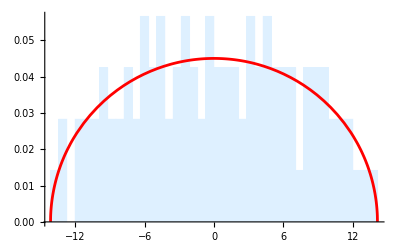

```mathematica
Show[Histogram[EigenvaluesGOE[100],{RadiusGOE[100]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGOE[x,100],{x,-RadiusGOE[100],RadiusGOE[100]},PlotStyle->{Red}],PlotRange->Full,AxesOrigin->{-RadiusGOE[100]-0.5,0}]
```

#### Probability Distribution Function Size=1000

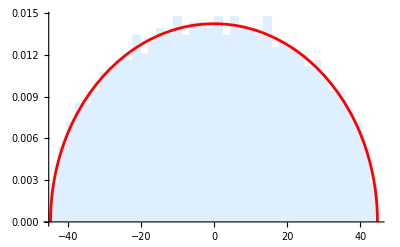

```mathematica
Show[Histogram[EigenvaluesGOE[1000],{RadiusGOE[1000]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGOE[x,1000],{x,-RadiusGOE[1000],RadiusGOE[1000]},PlotStyle->{Red}],PlotRange->Full,AxesOrigin->{-RadiusGOE[1000]-0.5,0}]
```

#### Probability Distribution Function Size=5000

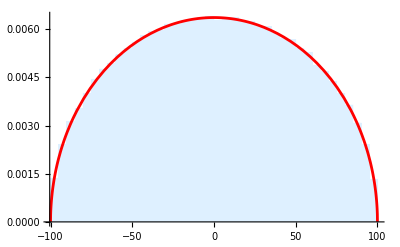

```mathematica
Show[Histogram[EigenvaluesGOE[5000],{RadiusGOE[5000]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGOE[x,5000],{x,-RadiusGOE[5000],RadiusGOE[5000]},PlotStyle->{Red}],PlotRange->Full,AxesOrigin->{-RadiusGOE[5000]-0.5,0}]
```

#### Cumulative Distribution Function Size=100

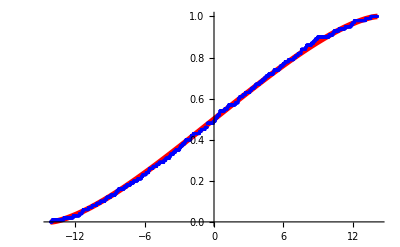

```mathematica
Show[Plot[CDFSemicircleGOE[x,100],{x,-RadiusGOE[100],RadiusGOE[100]},PlotStyle->{Thickness[0.01],Red}],ListPlot[Transpose[{Range[-RadiusGOE[100],RadiusGOE[100],RadiusGOE[100]/1000],CDensityGOE[100]}],PlotStyle->{Blue},Joined->False]]
```

#### Cumulative Distribution Function Size=1000

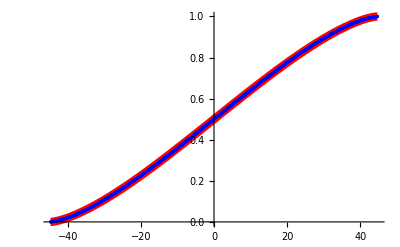

```mathematica
Show[Plot[CDFSemicircleGOE[x,1000],{x,-RadiusGOE[1000],RadiusGOE[1000]},PlotStyle->{Thickness[0.015],Red}],ListPlot[Transpose[{Range[-RadiusGOE[1000],RadiusGOE[1000],RadiusGOE[1000]/1000],CDensityGOE[1000]}],PlotStyle->{Blue},Joined->False]]
```

#### Cumulative Distribution Function Size=5000

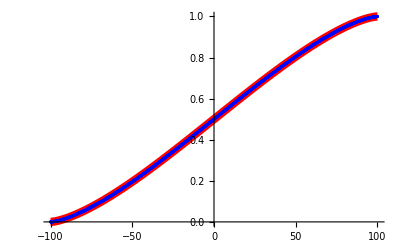

```mathematica
Show[Plot[CDFSemicircleGOE[x,5000],{x,-RadiusGOE[5000],RadiusGOE[5000]},PlotStyle->{Thickness[0.015],Red}],ListPlot[Transpose[{Range[-RadiusGOE[5000],RadiusGOE[5000],RadiusGOE[5000]/1000],CDensityGOE[5000]}],PlotStyle->{Blue},Joined->False]]
```

### Testing Wigner’s Surmise vs Unfolded Spacings:

```mathematica
WignerGOE[x_]:=(π/2) x Exp[-(π x^2/4)];(*Wigner's Surmise*)
```

```mathematica
Poisson[x_]:=Exp[-x];(*Poisson Distribution*)
```

#### Size=100

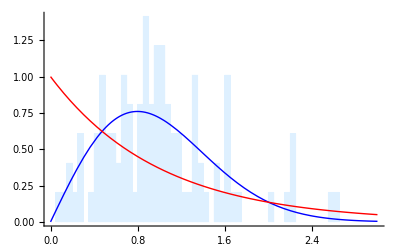

```mathematica
Show[Histogram[SpacingGOE[100],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGOE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}}],PlotRange->Full,AxesOrigin->{{-1,0}}]
```

#### Size=1000

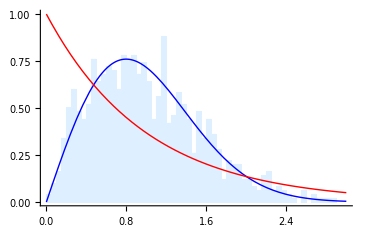

```mathematica
Show[Histogram[SpacingGOE[1000],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGOE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}}],PlotRange->Full,AxesOrigin->{{0,0}}]
```

#### Size=5000

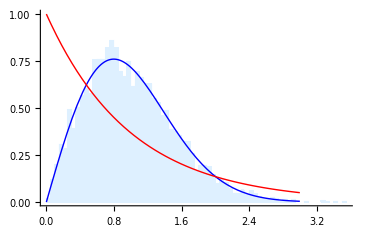

```mathematica
Show[Histogram[SpacingGOE[5000],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGOE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}}],PlotRange->Full,AxesOrigin->{{0,0}}]
```

## Tests GSE matrices

### Testing Wigner’s Semicircle Law:

#### Probability Distribution Function Size=100

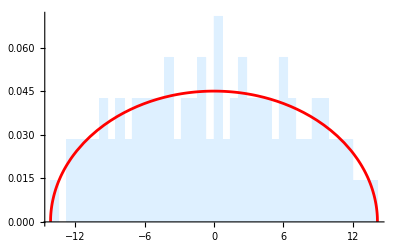

```mathematica
Show[Histogram[EigenvaluesGSE[100],{RadiusGSE[100]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGSE[x,100],{x,-RadiusGSE[100],RadiusGSE[100]},PlotStyle->{Red},PlotRange->{{-RadiusGSE[100]-0.5,RadiusGSE[100]+1},Automatic}],PlotRange->Full,AxesOrigin->{-RadiusGSE[100]-0.5,0}]
```

#### Probability Distribution Function Size=1000

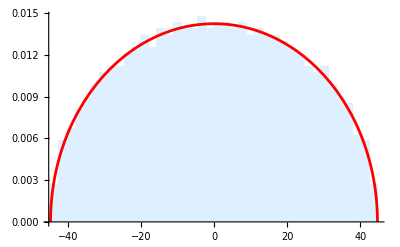

```mathematica
Show[Histogram[EigenvaluesGSE[1000],{RadiusGSE[1000]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGSE[x,1000],{x,-RadiusGSE[1000],RadiusGSE[1000]},PlotStyle->{Red}],PlotRange->Full,AxesOrigin->{-RadiusGSE[1000]-0.5,0}]
```

#### Probability Distribution Function Size=3000

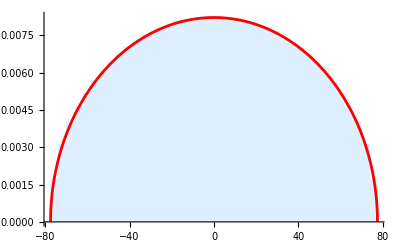

```mathematica
Show[Histogram[EigenvaluesGSE[3000],{RadiusGSE[3000]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGSE[x,3000],{x,-RadiusGSE[3000],RadiusGSE[3000]},PlotStyle->{Red}]]
```

#### Cumulative Distribution Function Size=100

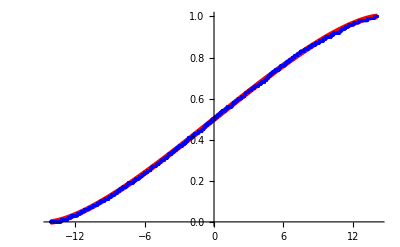

```mathematica
Show[Plot[CDFSemicircleGSE[x,100],{x,-RadiusGSE[100],RadiusGSE[100]},PlotStyle->{Thickness[0.01],Red}],ListPlot[Transpose[{Range[-RadiusGSE[100],RadiusGSE[100],RadiusGSE[100]/1000],CDensityGSE[100]}],PlotStyle->{Blue},Joined->False]]
```

#### Cumulative Distribution Function Size=1000

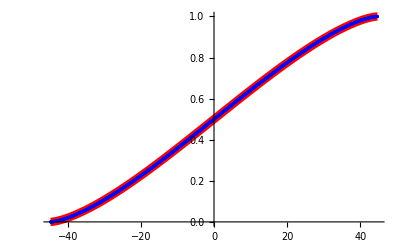

```mathematica
Show[Plot[CDFSemicircleGSE[x,1000],{x,-RadiusGSE[1000],RadiusGSE[1000]},PlotStyle->{Thickness[0.015],Red}],ListPlot[Transpose[{Range[-RadiusGSE[1000],RadiusGSE[1000],RadiusGSE[1000]/1000],CDensityGSE[1000]}],PlotStyle->{Blue},Joined->False]]
```

#### Cumulative Distribution Function Size=3000

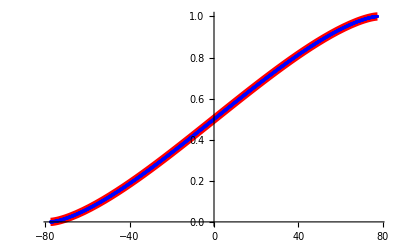

```mathematica
Show[Plot[CDFSemicircleGSE[x,3000],{x,-RadiusGSE[3000],RadiusGSE[3000]},PlotStyle->{Thickness[0.015],Red}],ListPlot[Transpose[{Range[-RadiusGSE[3000],RadiusGSE[3000],RadiusGSE[3000]/1000],CDensityGSE[3000]}],PlotStyle->{Blue},Joined->False]]
```

### Testing Wigner’s Surmise vs Unfolded Spacings:

```mathematica
Poisson[x_]:=Exp[-x];(*Poisson Distribution*)
WignerGSE[x_]:=2^18/(3^6 π^3)x^4 ⅇ^(-64 x^2/(9π)); (*I don't know here this comes from but it fits the distribution*)
```

#### Size=100

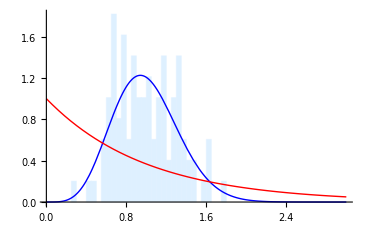

```mathematica
Show[Histogram[SpacingGSE[100],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGSE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}},PlotRange->Full],PlotRange->Full,AxesOrigin->{0,0}]
```

#### Size=1000

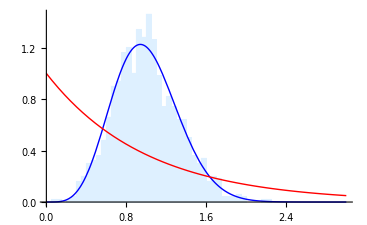

```mathematica
Show[Histogram[SpacingGSE[1000],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGSE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}},PlotRange->Full],PlotRange->Full,AxesOrigin->{0,0}]
```

#### Size=3000

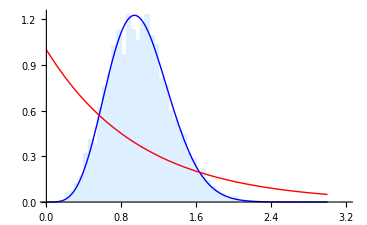

```mathematica
Show[Histogram[SpacingGSE[3000],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGSE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}},PlotRange->Full],PlotRange->Full,AxesOrigin->{0,0},PlotRange->Full,AxesOrigin->{0,0}]
```

## Tests GUE matrices

### Testing Wigner’s Semicircle Law:

#### Probability Distribution Function Size=100

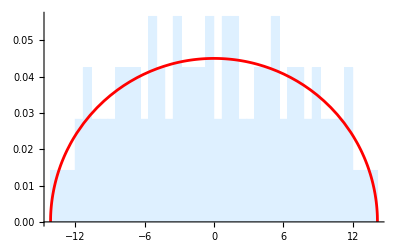

```mathematica
Show[Histogram[EigenvaluesGUE[100],{RadiusGUE[100]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGUE[x,100],{x,-RadiusGUE[100],RadiusGUE[100]},PlotStyle->{Red}]]
```

#### Probability Distribution Function Size=1000

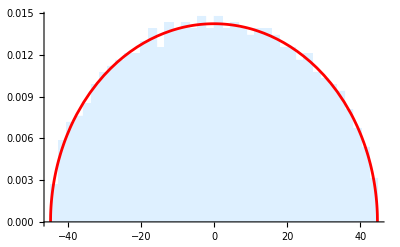

```mathematica
Show[Histogram[EigenvaluesGUE[1000],{RadiusGUE[1000]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGUE[x,1000],{x,-RadiusGUE[1000],RadiusGUE[1000]},PlotStyle->{Red}]]
```

#### Probability Distribution Function Size=3000

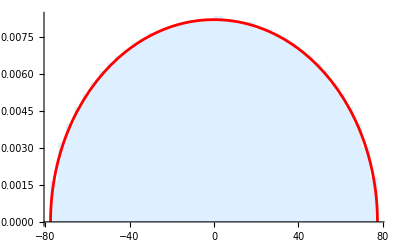

```mathematica
Show[Histogram[EigenvaluesGSE[3000],{RadiusGUE[3000]/20},"PDF",ChartStyle->LightBlue],Plot[SemicircleGUE[x,3000],{x,-RadiusGUE[3000],RadiusGUE[3000]},PlotStyle->{Red}]]
```

#### Cumulative Distribution Function Size=100

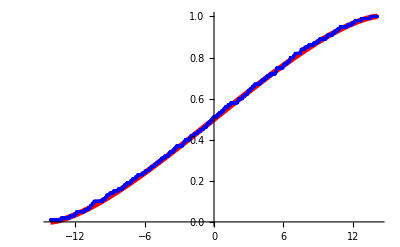

```mathematica
Show[Plot[CDFSemicircleGUE[x,100],{x,-RadiusGUE[100],RadiusGUE[100]},PlotStyle->{Thickness[0.01],Red}],ListPlot[Transpose[{Range[-RadiusGUE[100],RadiusGUE[100],RadiusGUE[100]/1000],CDensityGUE[100]}],PlotStyle->{Blue},Joined->False]]
```

#### Cumulative Distribution Function Size=1000

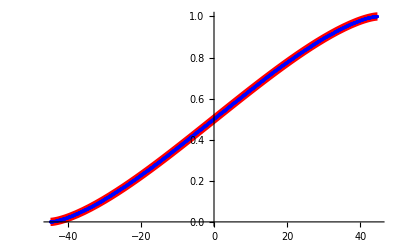

```mathematica
Show[Plot[CDFSemicircleGUE[x,1000],{x,-RadiusGUE[1000],RadiusGUE[1000]},PlotStyle->{Thickness[0.015],Red}],ListPlot[Transpose[{Range[-RadiusGUE[1000],RadiusGUE[1000],RadiusGUE[1000]/1000],CDensityGUE[1000]}],PlotStyle->{Blue},Joined->False]]
```

#### Cumulative Distribution Function Size=3000

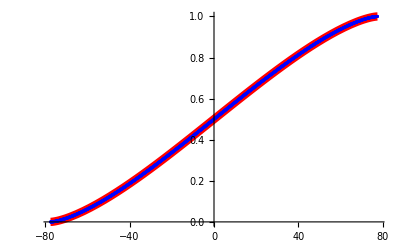

```mathematica
Show[Plot[CDFSemicircleGUE[x,3000],{x,-RadiusGUE[3000],RadiusGUE[3000]},PlotStyle->{Thickness[0.015],Red}],ListPlot[Transpose[{Range[-RadiusGUE[3000],RadiusGUE[3000],RadiusGUE[3000]/1000],CDensityGUE[3000]}],PlotStyle->{Blue},Joined->False]]
```

### Testing Wigner’s Surmise vs Unfolded Spacings:

```mathematica
WignerGUE[x_]:=(32/π^2) x^2 Exp[-(4 x^2/π)];(*Wigner's Surmise*)
Poisson[x_]:=Exp[-x];(*Poisson Distribution*)
```

#### Size=100

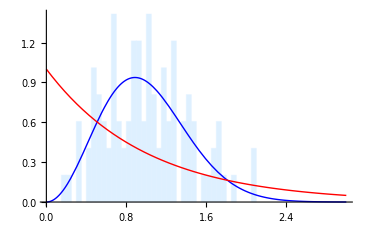

```mathematica
Show[Histogram[SpacingGUE[100],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGUE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}},PlotRange->Full],PlotRange->Full,AxesOrigin->{0,0}]
```

#### Size=1000

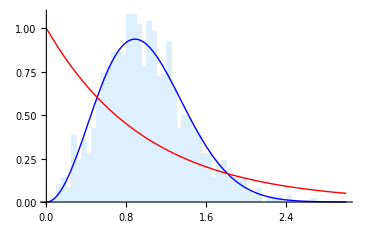

```mathematica
Show[Histogram[SpacingGUE[1000],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGUE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}},PlotRange->Full],PlotRange->Full,AxesOrigin->{0,0}]
```

#### Size=3000

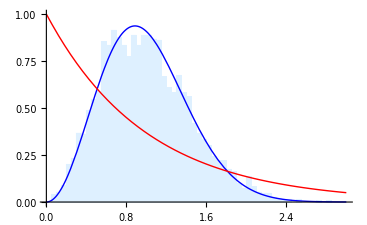

```mathematica
Show[Histogram[SpacingGUE[3000],{0.05},"PDF",ChartStyle->LightBlue],Plot[{WignerGUE[x],Poisson[x]},{x,0,3},PlotStyle->{{Thick, Blue},{Thick,Red}},PlotRange->Full],PlotRange->Full,AxesOrigin->{0,0}]
```